```mathematica
Ang = Range[-Pi/2 , Pi/2,0.1]
```

{-1.5708,-1.4708,-1.3708,-1.2708,-1.1708,-1.0708,-0.970796,-0.870796,-0.770796,-0.670796,-0.570796,-0.470796,-0.370796,-0.270796,-0.170796,-0.0707963,0.0292037,0.129204,0.229204,0.329204,0.429204,0.529204,0.629204,0.729204,0.829204,0.929204,1.0292,1.1292,1.2292,1.3292,1.4292,1.5292}

```mathematica
T = (Cos[Ang]^2)
```

{3.7494×10^-33,0.00996671,0.0394695,0.0873322,0.151647,0.229849,0.318821,0.415016,0.5146,0.613601,0.708073,0.794251,0.868697,0.928444,0.971111,0.994996,0.999147,0.983399,0.948379,0.895484,0.826822,0.74513,0.653666,0.556076,0.456251,0.358169,0.265742,0.182654,0.112217,0.0572402,0.0199149,0.00172895}

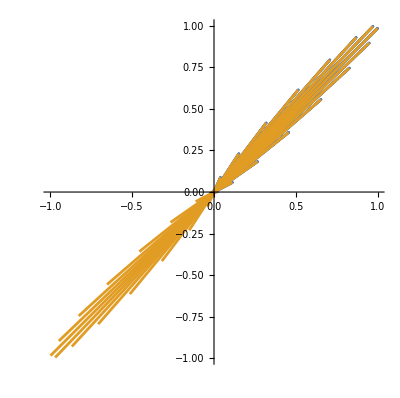

Syntax::sntxf: "PolarPlot[T," cannot be followed by "[Ang,-Pi/2,Pi/2]]".

PolarPlot::pllim: Range specification Ang is not of the form {x, xmin, xmax}.

PolarPlot::pllim: Range specification Theta is not of the form {x, xmin, xmax}.

```mathematica
PolarPlot[T,{Ang,-Pi/2 , Pi/2}]
```